```mathematica
a=Import["~/Ex3_2025-12-31_H07_M38_S11/Ex3_2025-12-31_H07_M38_S11.csv"];
```

```mathematica
a[[1]]
```

{2025 Dec 31 07:38:14.260,3.07,-0.25,0.,1}

```mathematica
b1=Table[{a[[i,2]],a[[i,3]]},{i,Length[a]}];
```

```mathematica
b2=Table[{a[[i,2]],a[[i,4]]},{i,Length[a]}];
```

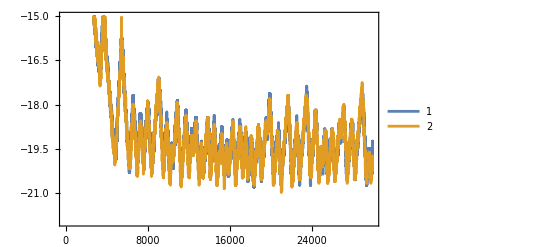

```mathematica
ListPlot[{b1,b2},Joined->True,PlotRange->{-15,-22},Axes->False,Frame->True,PlotLegends->Automatic]
```

```mathematica
c1=Table[a[[i,3]],{i,Length[a]}];
```

```mathematica
c2=Table[a[[i,4]],{i,Length[a]}];
```

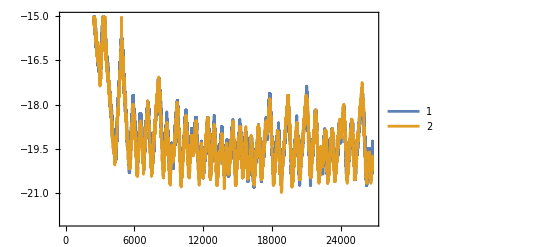

```mathematica
ListPlot[{c1,c2},Joined->True,PlotRange->{-15,-22},Axes->False,Frame->True,PlotLegends->Automatic]
```

```mathematica
c=Table[a[[i,4]],{i,10000,25000}];
```

```mathematica
mx=
Max[c]
```

-17.6875

```mathematica
mn=Min[c]
```

-21.

```mathematica
mx-mn
```

3.3125

```mathematica
c3=Table[a[[i,5]],{i,Length[a]}];
```

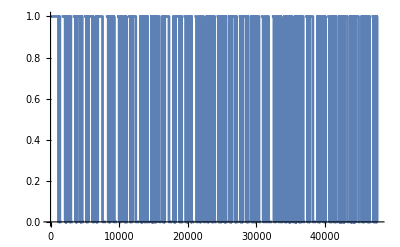

```mathematica
ListPlot[c3,Joined->True]
```

```mathematica
Length[c3]
```

47649

```mathematica
??Sum
```

```mathematica
in=Length[c3]
```

47649

```mathematica
Sum[c3[[i]],{i,in}]
```

26725+29

```mathematica
c3[[Length[c3]]]
```

0

```mathematica
Sum[c3[[i]],{i,in}]/Length[c3]//N
```

0.0000209868 (26725.+29. )